```mathematica
n=2;
```

```mathematica
σ=(3/4((2n+1)/(1+n)^2 ϕ[x]+ϕ''[x])^2+3(n/(n+1)ϕ'[x])^2)^(1/2)
```

√(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2)

```mathematica
hrr={(n(n+2))/(1+n)^2 σ^(n-1)((2n+1)/(1+n)^2 ϕ[x]+ϕ''[x])+D[σ^(n-1)((2n+1)/(1+n)^2 ϕ[x]+ϕ''[x]),{x,2}]+(4n)/(1+n)^2 D[σ^(n-1)ϕ'[x],x]==0,ϕ[0]==1,ϕ'[0]==0,ϕ''[0]==a,ϕ'''[0]==0}
```

{8/9 ((5 ϕ[x])/9+ϕ''[x]) √(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2)+(((5 ϕ'[x])/9+ϕ^(3)[x]) (8/3 ϕ'[x] ϕ''[x]+3/2 ((5 ϕ[x])/9+ϕ''[x]) ((5 ϕ'[x])/9+ϕ^(3)[x])))/(√(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2))+8/9 (ϕ''[x] √(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2)+(ϕ'[x] (8/3 ϕ'[x] ϕ''[x]+3/2 ((5 ϕ[x])/9+ϕ''[x]) ((5 ϕ'[x])/9+ϕ^(3)[x])))/(2 √(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2)))+√(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2) ((5 ϕ''[x])/9+ϕ^(4)[x])+((5 ϕ[x])/9+ϕ''[x]) (-((8/3 ϕ'[x] ϕ''[x]+3/2 ((5 ϕ[x])/9+ϕ''[x]) ((5 ϕ'[x])/9+ϕ^(3)[x]))^2)/(4 (4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2)^(3/2))+(8/3 ϕ''[x]^2+8/3 ϕ'[x] ϕ^(3)[x]+3/2 ((5 ϕ'[x])/9+ϕ^(3)[x])^2+3/2 ((5 ϕ[x])/9+ϕ''[x]) ((5 ϕ''[x])/9+ϕ^(4)[x]))/(2 √(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2)))==0,ϕ[0]==1,ϕ'[0]==0,ϕ''[0]==a,ϕ^(3)[0]==0}

```mathematica
sol=ParametricNDSolve[hrr,ϕ,{x,0,π},a]
```

{ϕ→ParametricFunction[<>]}

```mathematica
boundaryval[a_?NumericQ]:=ϕ[a][π]/.sol
```

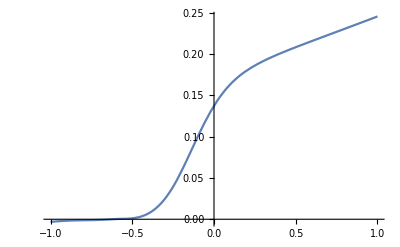

```mathematica
Plot[boundaryval[a],{a,-1,1}]
```

```mathematica
a1=a/.FindRoot[boundaryval[a]==0,{a,-0.5}]
```

-0.620644

```mathematica
hrr1={(n(n+2))/(1+n)^2 σ^(n-1)((2n+1)/(1+n)^2 ϕ[x]+ϕ''[x])+D[σ^(n-1)((2n+1)/(1+n)^2 ϕ[x]+ϕ''[x]),{x,2}]+(4n)/(1+n)^2 D[σ^(n-1)ϕ'[x],x]==0,ϕ[0]==1,ϕ'[0]==0,ϕ''[0]==a1,ϕ'''[0]==0}
```

{8/9 ((5 ϕ[x])/9+ϕ''[x]) √(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2)+(((5 ϕ'[x])/9+ϕ^(3)[x]) (8/3 ϕ'[x] ϕ''[x]+3/2 ((5 ϕ[x])/9+ϕ''[x]) ((5 ϕ'[x])/9+ϕ^(3)[x])))/(√(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2))+8/9 (ϕ''[x] √(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2)+(ϕ'[x] (8/3 ϕ'[x] ϕ''[x]+3/2 ((5 ϕ[x])/9+ϕ''[x]) ((5 ϕ'[x])/9+ϕ^(3)[x])))/(2 √(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2)))+√(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2) ((5 ϕ''[x])/9+ϕ^(4)[x])+((5 ϕ[x])/9+ϕ''[x]) (-((8/3 ϕ'[x] ϕ''[x]+3/2 ((5 ϕ[x])/9+ϕ''[x]) ((5 ϕ'[x])/9+ϕ^(3)[x]))^2)/(4 (4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2)^(3/2))+(8/3 ϕ''[x]^2+8/3 ϕ'[x] ϕ^(3)[x]+3/2 ((5 ϕ'[x])/9+ϕ^(3)[x])^2+3/2 ((5 ϕ[x])/9+ϕ''[x]) ((5 ϕ''[x])/9+ϕ^(4)[x]))/(2 √(4/3 ϕ'[x]^2+3/4 ((5 ϕ[x])/9+ϕ''[x])^2)))==0,ϕ[0]==1,ϕ'[0]==0,ϕ''[0]==-0.620644,ϕ^(3)[0]==0}

```mathematica
sol1=NDSolve[hrr1,ϕ,{x,0,π}]
```

{{ϕ→InterpolatingFunction[…]}}

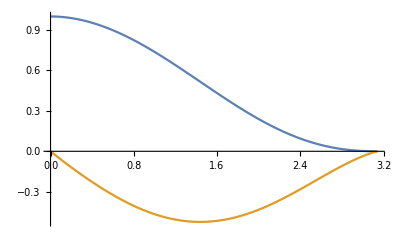

```mathematica
Plot[ {ϕ[x]/.sol1,ϕ'[x]/.sol1},{x,0,π}]
```

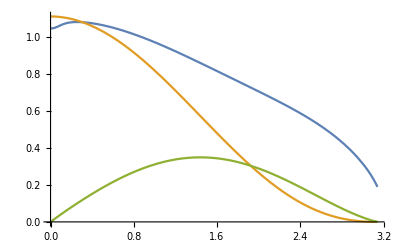

```mathematica
Plot[{((1+2n)/(1+n)ϕ[x]+ ϕ''[x])/.sol1,((1+2n)n)/(1+n)^2 ϕ[x]/.sol1,-n/(n+1)ϕ'[x]/.sol1},{x,0,π}]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
n=10;
```

```mathematica
σ=(3/4((2n+1)/(1+n)^2 ϕ[x]+ϕ''[x])^2+3(n/(n+1)ϕ'[x])^2)^(1/2)
```

√(300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)

```mathematica
hrr={(n(n+2))/(1+n)^2 σ^(n-1)((2n+1)/(1+n)^2 ϕ[x]+ϕ''[x])+D[σ^(n-1)((2n+1)/(1+n)^2 ϕ[x]+ϕ''[x]),{x,2}]+(4n)/(1+n)^2 D[σ^(n-1)ϕ'[x],x]==0,ϕ[0]==1,ϕ'[0]==0,ϕ''[0]==a,ϕ'''[0]==0}
```

{120/121 ((21 ϕ[x])/121+ϕ''[x]) (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(9/2)+9 (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(7/2) ((21 ϕ'[x])/121+ϕ^(3)[x]) (600/121 ϕ'[x] ϕ''[x]+3/2 ((21 ϕ[x])/121+ϕ''[x]) ((21 ϕ'[x])/121+ϕ^(3)[x]))+40/121 (ϕ''[x] (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(9/2)+9/2 ϕ'[x] (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(7/2) (600/121 ϕ'[x] ϕ''[x]+3/2 ((21 ϕ[x])/121+ϕ''[x]) ((21 ϕ'[x])/121+ϕ^(3)[x])))+(300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(9/2) ((21 ϕ''[x])/121+ϕ^(4)[x])+((21 ϕ[x])/121+ϕ''[x]) (63/4 (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(5/2) (600/121 ϕ'[x] ϕ''[x]+3/2 ((21 ϕ[x])/121+ϕ''[x]) ((21 ϕ'[x])/121+ϕ^(3)[x]))^2+9/2 (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(7/2) (600/121 ϕ''[x]^2+600/121 ϕ'[x] ϕ^(3)[x]+3/2 ((21 ϕ'[x])/121+ϕ^(3)[x])^2+3/2 ((21 ϕ[x])/121+ϕ''[x]) ((21 ϕ''[x])/121+ϕ^(4)[x])))==0,ϕ[0]==1,ϕ'[0]==0,ϕ''[0]==a,ϕ^(3)[0]==0}

```mathematica
sol=ParametricNDSolve[hrr,ϕ,{x,0,π},a]
```

{ϕ→ParametricFunction[<>]}

```mathematica
boundaryval[a_?NumericQ]:=ϕ[a][π]/.sol
```

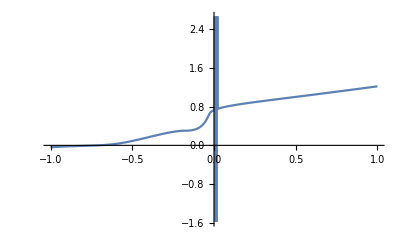

```mathematica
Plot[boundaryval[a],{a,-1,1}]
```

```mathematica
a1=a/.FindRoot[boundaryval[a]==0,{a,-0.7}]
```

-0.710573

```mathematica
hrr1={(n(n+2))/(1+n)^2 σ^(n-1)((2n+1)/(1+n)^2 ϕ[x]+ϕ''[x])+D[σ^(n-1)((2n+1)/(1+n)^2 ϕ[x]+ϕ''[x]),{x,2}]+(4n)/(1+n)^2 D[σ^(n-1)ϕ'[x],x]==0,ϕ[0]==1,ϕ'[0]==0,ϕ''[0]==a1,ϕ'''[0]==0}
```

{120/121 ((21 ϕ[x])/121+ϕ''[x]) (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(9/2)+9 (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(7/2) ((21 ϕ'[x])/121+ϕ^(3)[x]) (600/121 ϕ'[x] ϕ''[x]+3/2 ((21 ϕ[x])/121+ϕ''[x]) ((21 ϕ'[x])/121+ϕ^(3)[x]))+40/121 (ϕ''[x] (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(9/2)+9/2 ϕ'[x] (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(7/2) (600/121 ϕ'[x] ϕ''[x]+3/2 ((21 ϕ[x])/121+ϕ''[x]) ((21 ϕ'[x])/121+ϕ^(3)[x])))+(300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(9/2) ((21 ϕ''[x])/121+ϕ^(4)[x])+((21 ϕ[x])/121+ϕ''[x]) (63/4 (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(5/2) (600/121 ϕ'[x] ϕ''[x]+3/2 ((21 ϕ[x])/121+ϕ''[x]) ((21 ϕ'[x])/121+ϕ^(3)[x]))^2+9/2 (300/121 ϕ'[x]^2+3/4 ((21 ϕ[x])/121+ϕ''[x])^2)^(7/2) (600/121 ϕ''[x]^2+600/121 ϕ'[x] ϕ^(3)[x]+3/2 ((21 ϕ'[x])/121+ϕ^(3)[x])^2+3/2 ((21 ϕ[x])/121+ϕ''[x]) ((21 ϕ''[x])/121+ϕ^(4)[x])))==0,ϕ[0]==1,ϕ'[0]==0,ϕ''[0]==-0.710573,ϕ^(3)[0]==0}

```mathematica
sol1=NDSolve[hrr1,ϕ,{x,0,π}]
```

{{ϕ→InterpolatingFunction[…]}}

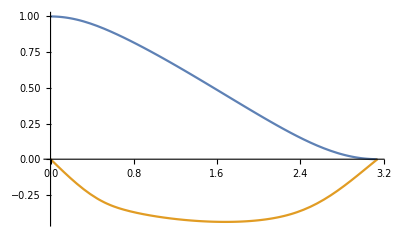

```mathematica
Plot[ {ϕ[x]/.sol1,ϕ'[x]/.sol1},{x,0,π}]
```

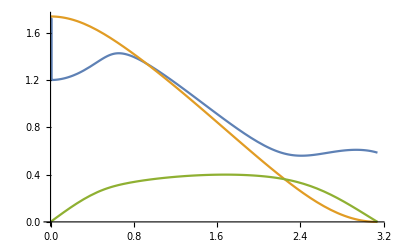

```mathematica
Plot[{((1+2n)/(1+n)ϕ[x]+ ϕ''[x])/.sol1,((1+2n)n)/(1+n)^2 ϕ[x]/.sol1,-n/(n+1)ϕ'[x]/.sol1},{x,0,π}]
```